```mathematica
ztw
```

```mathematica
langer[x_,alfa_]:=x^2+alfa*x^4
doublewell[x_]:=(1/4)*(x^2-1)^2
paper[a_,mu_,x_]:=-(mu^2/(2*a^2))*(x^2-a^2)^2+mu^2*a^4/(2*a^2)
paperone[a_,mu_,x_]:=(mu^2/(2*a^2))*(x^2-a^2)^2
```

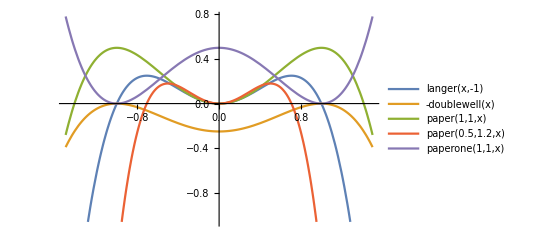

```mathematica
Plot[{langer[x,-1],-doublewell[x], paper[1,1,x],paper[0.5,1.2,x],paperone[1,1,x]},{x,-1.5,1.5}, PlotLegends->"Expressions"]
```

```mathematica
langerstat[x_,alfa_]:=Sqrt[1/-alfa]*Sech[Sqrt[2]*x]
```

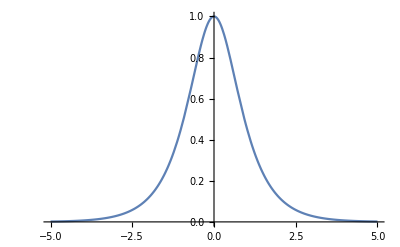

```mathematica
Plot[langerstat[x,-1],{x,-5,5}]
```

```mathematica
bubbleone[x_,alfa_]:=Sqrt[3/4]*2^(1/4)*(Sech[x*Sqrt[2]])^2
```

```mathematica
bubbletwo[x_,alfa_]:=Sqrt[3/4]*2^(1/4)*Sinh[Sqrt[2]*x]/(Cosh[Sqrt[2]*x])^2
```

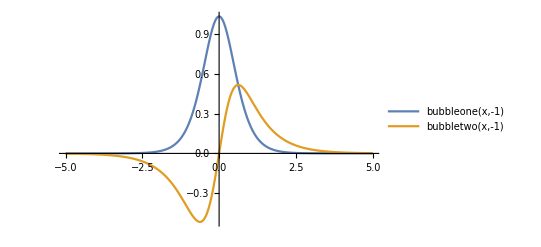

```mathematica
Plot[{bubbleone[x,-1],bubbletwo[x,-1]},{x,-5,5},PlotLegends->"Expressions", PlotRange->All]
```

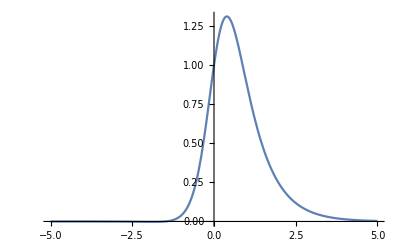

```mathematica
Plot[{langerstat[x,-1]+bubbletwo[x,-1]},{x,-5,5},PlotLegends->"Expressions"]
```

```mathematica
period[a_,k_,mu_,x_]:=(a*(1+k)/Sqrt[1+k^2])*JacobiDN[(mu/a)*(a*(1+k)/Sqrt[1+k^2])*x,k]
```

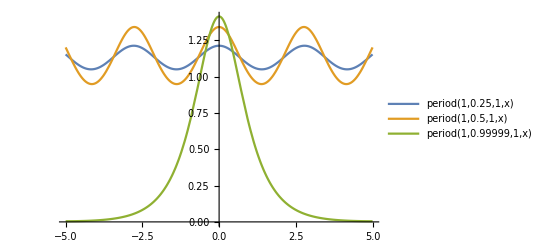

```mathematica
Plot[{period[1,0.25,1,x],period[1,0.5,1,x],period[1,0.99999,1,x]},{x,-5,5}, PlotLegends->"Expressions"]
```

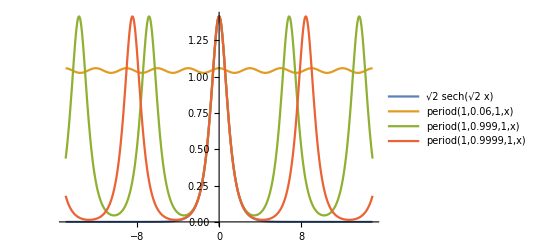

```mathematica
Plot[{1*Sqrt[2]*Sech[1*Sqrt[2]*x],period[1,0.06,1,x],period[1,0.999,1,x],period[1,0.9999,1,x]},{x,-15,15}, PlotLegends->"Expressions"]
```

```mathematica
leng[a_,k_,mu_,n_]:=2*n*EllipticK[k]/((mu/a)*(a*(1+k)/Sqrt[1+k^2]))
```

```mathematica
leng[1,2,1,1]//N
```

1.95437-1.95437 ⅈ

```mathematica
period[1,2,1,1]//N
```

-0.0410703+1.15241×10^-16 ⅈ

```mathematica
period[1,2,1,1+3*leng[1,2,1,1]]//N
```

-0.0410703+1.15241×10^-16 ⅈ

```mathematica
EllipticK[0]
```

π/2

```mathematica
len1[k_,n_,mu_]:=4*EllipticK[k]*n/(Sqrt[2/(1+k^2)]*mu)
len2[a_, k_,n_,mu_]:=2*EllipticK[k]*n/(    mu*(1+k)/Sqrt[1+k^2])
```

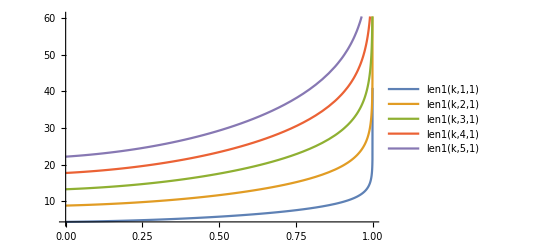

```mathematica
Plot[{len1[k,1,1],len1[k,2,1],len1[k,3,1],len1[k,4,1],len1[k,5,1]},{k,0,1}, PlotLegends->"Expressions"]
```

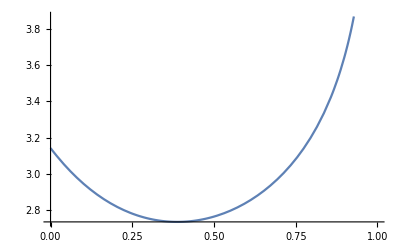

```mathematica
Plot[{len2[1,k,1,1]},{k,0,1}, PlotLegends->"Expressions"]
```

```mathematica
len2[1,0,2,1]
```

2 π

```mathematica
FindRoot[len2[1,k,2,1]-3,{k,0.0}]
FindRoot[len2[1,k,2,1]-3,{k,0.99}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{k→0.38784}

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{k→0.387839}

```mathematica
len2[1,0.387841,2,1]//N
```

5.46916

```mathematica
{len2[1,0.2,1,4],len2[1,0.58,1,4]}
```

{11.2833,11.2883}

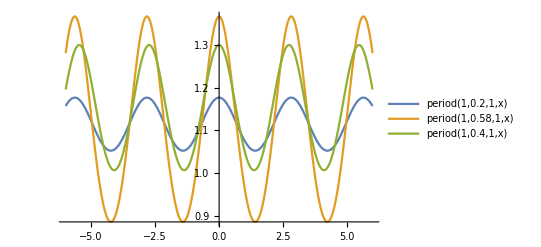

```mathematica
Plot[{period[1,0.2,1,x],period[1,0.58,1,x],period[1,0.4,1,x]},{x,-6,6}, PlotLegends->"Expressions"]
```

```mathematica
rootsk[L_?NumericQ,a_?NumericQ, n_?NumericQ ,mu_?NumericQ]:=NSolve[{len2[a,k,n,mu]==L,0≤k≤1},k]
```

```mathematica
FindRoot[len1[k,4,1]-20,{k,0.999}]
```

{k→0.279923}

```mathematica
len1[0.279923,4,1]//N
```

20.

```mathematica
Table[i^2,{i,1,10}]
```

{1,4,9,16,25,36,49,64,81,100}

```mathematica
Table[FindRoot[len1[k,i,1]-30,{k,0.999}],{i,1,5}]
```

{{k→0.999995},{k→0.991331},{k→0.908017},{k→0.737264},{k→0.526411}}

```mathematica
Values@Table[FindRoot[len1[k,i,1]-30,{k,0.999}],{i,1,Floor[8/3]}]
```

{{0.999995},{0.991331}}

```mathematica
period[a_,k_,mu_,x_]:=(a*(1+k)/Sqrt[1+k^2])*JacobiDN[(mu/a)*(a*(1+k)/Sqrt[1+k^2])*x,k]
```

```mathematica
NIntegrate[period[1,Values@Table[FindRoot[len1[k,i,1]-30,{k,0.999}],{i,1,Floor[12/3]}][[1]],1,x],{x,0,30}]
```

{8.00618}

```mathematica
NIntegrate[period[1,Values@Table[FindRoot[len1[k,i,1]-30,{k,0.999}],{i,1,Floor[12/3]}][[2]],1,x],{x,0,30}]
```

{17.3875}

```mathematica
NIntegrate[period[1,Values@Table[FindRoot[len1[k,i,1]-30,{k,0.999}],{i,1,Floor[12/3]}][[3]],1,x],{x,0,30}]
```

{25.6127}

```mathematica
NIntegrate[period[1,Values@Table[FindRoot[len1[k,i,1]-30,{k,0.999}],{i,1,Floor[12/3]}],1,x],{x,0,30}]
```

{{8.00618},{17.3875},{25.6127},{30.7229}}

```mathematica
{{8.006184861347753},{17.387543462849507},{25.612656818900764},{30.722912534602482}}

autoval1[k_,mu_]:=-3*mu^2*(1+k)^2/(1+k^2)
```

{{8.00618},{17.3875},{25.6127},{30.7229}}

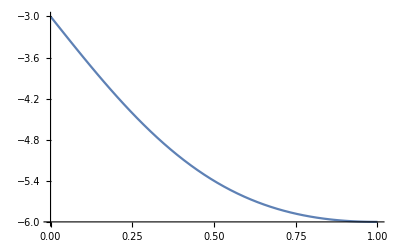

```mathematica
Plot[autoval1[k,1],{k,0,1}]
```

```mathematica
Theta[L_,T_,mu_,a_,guess_]:=NIntegrate[period[a,Values@Table[FindRoot[len2[a,k,i,1]-L,{k,guess}],{i,1,Floor[L/(π/mu)]}],mu,x],{x,0,L}]-T*Log[Sqrt[T/(-autoval1[Values@Table[FindRoot[len2[a,k,i,1]-L,{k,guess}],{i,1,Floor[L/(π/mu)]}],mu])]]

Kvalues[L_,T_,mu_,a_,guess_]:=Values@Table[FindRoot[len2[a,k,i,1]-L,{k,guess}],{i,1,Floor[L/(π/mu)]}]
```

```mathematica
Kvalues[3.15,3,1,1,0.99]


rootsk[3,1,1,1]
```

{{0.778155}}

{{k→0.0682733},{k→0.710837}}

```mathematica
Theta1[L_,T_,mu_,a_,guess_]:=NIntegrate[period[a,Values@Table[FindRoot[len2[a,k,i,1]-L,{k,guess}],{i,1,Floor[L/(π/mu)]}],mu,x],{x,0,L}]/T
```

```mathematica
a = Theta1[20,2,1,1,0.1]
```

{{1.5708},{3.14159},{4.71239},{6.28319},{7.85398},{9.42478}}

```mathematica
Position[Theta[30,200,1,1,0.1],Min[Theta[30,200,1,1,0.1]]]
```

{{1,1}}

```mathematica
ThetaD[L_,T_,mu_,a_,guess_]:=NIntegrate[  
0.5*(D [period[a,Values@Table[FindRoot[len2[a,k,i,1]-L,{k,guess}],{i,1,Floor[L/(π/mu)]}],mu,x],x])^2+paper[a,mu,x],{x,0,L}]-T*Log[Sqrt[T/(-autoval1[Values@Table[FindRoot[len2[a,k,i,1]-L,{k,guess}],{i,1,Floor[L/(π/mu)]}],mu])]]
```

```mathematica
ThetaD[20,1,1,1,0.9]
```

{{2.7815+1.55191×10^-29 ⅈ},{4.66708+9.58045×10^-24 ⅈ},{6.54725},{8.35921},{9.89037},{10.7316}}

```mathematica
ThetaD[L_,T_,mu_,a_,guess_]:=NIntegrate[  
0.5*(D[period[a,Values@Table[FindRoot[len2[a,k,i,1]-L,{k,guess}],{i,1,Floor[L/(π/mu)]}],mu,x],x])^2+paper[1,1,period[a,Values@Table[FindRoot[len2[a,k,i,1]-L,{k,guess}],{i,1,Floor[L/(π/mu)]}],mu,x]],{x,0,L}]-T*Log[Sqrt[T/(-autoval1[Values@Table[FindRoot[len2[a,k,i,1]-L,{k,guess}],{i,1,Floor[L/(π/mu)]}],mu])]]
```

```mathematica
ThetaD[20,3,1,1,0.5]
```

{{2.92534-5.35643×10^-28 ⅈ},{4.81092+3.39804×10^-23 ⅈ},{6.69109+8.53313×10^-20 ⅈ},{8.503},{10.0333},{10.8674}}

```mathematica
Kvalues[20,3,1,1,0.2]
```

{{-0.825739},{-0.668828},{-0.522652},{-0.380781},{-0.235205},{-0.0713332}}

```mathematica
energies[L_,T_,mu_,a_,guess_] := NIntegrate[  
0.5*(D[period[a,Values@Table[FindRoot[len2[a,k,i,1]-L,{k,guess}],{i,1,Floor[L/(π/mu)]}],mu,x],x])^2+paper[1,1,period[a,Values@Table[FindRoot[len2[a,k,i,1]-L,{k,guess}],{i,1,Floor[L/(π/mu)]}],mu,x]],{x,0,L}]
```

```mathematica
energies[20,40,1,1,0.99]
```

{{1.88562},{3.7712},{5.65137},{7.46335},{8.99495},{9.83966}}

```mathematica
energies[20,4000,1,1,0.05]
```

{{0.492812},{1.89102},{3.96718},{6.35261},{8.53853},{9.87545}}

```mathematica
ThetaDIMPRO[L_,T_,mu_,a_,guess_]:=NIntegrate[  
0.5*(D[period[a,Values@Table[rootsk[L,1,i,1],{i,1,Floor[L/(π/mu)]}],mu,x],x])^2+paper[1,1,period[a,Values@Table[FindRoot[len2[a,k,i,1]-L,{k,guess}],{i,1,Floor[L/(π/mu)]}],mu,x]],{x,0,L}]-T*Log[Sqrt[T/(-autoval1[Values@Table[rootsk[L,1,i,1],{i,1,Floor[L/(π/mu)]}],mu])]]
```

```mathematica
KvaluesIMPRO[L_,T_,mu_,a_,guess_]:=Values@Table[rootsk[L,1,i,1],{i,1,Floor[L/(π/mu)]}]
```

```mathematica
KvaluesIMPRO[20,3,1,1,0.2]
```

{{{1.}},{{0.999988}},{{0.99871}},{{0.986167}},{{0.940791}},{{0.835913}}}

```mathematica
ThetaDIMPRO[20,30000,1,1,0.5]
```

{{{-127756.}},{{-127754.}},{{-127752.}},{{-127751.}},{{-127763.}},{{-127867.}}}

```mathematica
KvaluesIMPRO[20,30000,1,1,0.5]
```

{{{1.}},{{0.999988}},{{0.99871}},{{0.986167}},{{0.940791}},{{0.835913}}}

```mathematica
energiesIMPRO[L_,T_,mu_,a_,guess_] := NIntegrate[  
0.5*(D[period[a,Values@Table[rootsk[L,1,i,1],{i,1,Floor[L/(π/mu)]}],mu,x],x])^2+paper[1,1,period[a,Values@Table[rootsk[L,1,i,1],{i,1,2}],mu,x]],{x,0,L}]
```

```mathematica
energyconfig[L_,mu_,a_,k_]:=NIntegrate[  
0.5*(D[period[a,k,mu,x],x])^2+paper[a,mu,period[a,k,mu,x]],{x,0,L}]
```

```mathematica
energyconfig[10,1,1,0.0]//N
```

5.

```mathematica
energyconfig[10,1,1,1]
```

0.942809

```mathematica
period[1,1,1,0]
```

√2

```mathematica
paper[1,1,1]
```

1/2

```mathematica
1/Sqrt[2]//N
```

0.707107

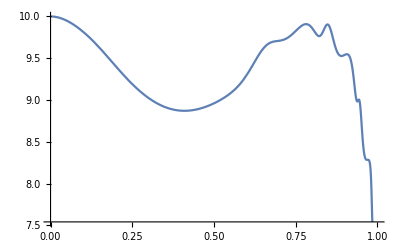

```mathematica
Plot[energyconfig[20,1,1,k],{k,0,1}, PlotPoints->20]
```

```mathematica
energyconfig[20,1,1,0.92]
```

9.45302

```mathematica
f = Table[energyconfig[20,1,1,0.05*i],{i,20}]
```

{9.94848,9.81535,9.62505,9.40256,9.19093,9.02412,8.91653,8.87274,8.8906,8.96108,9.0806,9.29971,9.61265,9.70959,9.82658,9.8614,9.89865,9.54107,8.79887,0.942809}

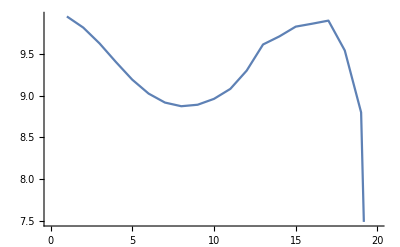

```mathematica
ListLinePlot[f]
```

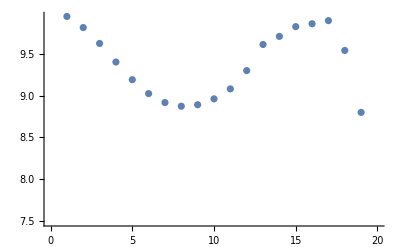

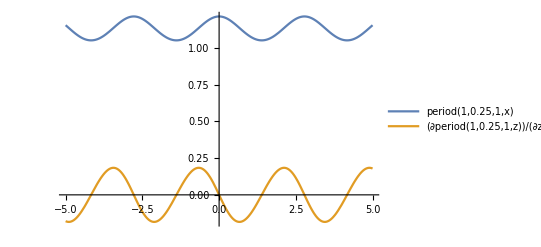

```mathematica
ListPlot[f]

Plot[{period[1,0.25,1,x],D[period[1,0.25,1,z],z]/.z->x},{x,-5,5}, PlotLegends->"Expressions"]
```

```mathematica
hj[x_]:=D[period[1,0.25,1,z],z]/.z->x
```

```mathematica
hj[2]//N
```

0.177515

```mathematica
period[1,0.25,1,1]
```

1.07809

```mathematica
LJder[delta_,p_]:=D[LJ[delta,z],z]/.z->p
```

```mathematica
w1[k_,mu_]:=-3*mu^2*(1-k)^2/(1+k^2)
```

```mathematica
w2[k_,mu_]:=-3*mu^2*(1+k)^2/(1+k^2)
w3[k_,mu_]:=-2*mu^2-2*mu^2*(Sqrt[1+14k^2+k^4])/(1+k^2)
```

```mathematica
w4[k_,mu_]:=-2*mu^2+2*mu^2*(Sqrt[1+14k^2+k^4])/(1+k^2)
```

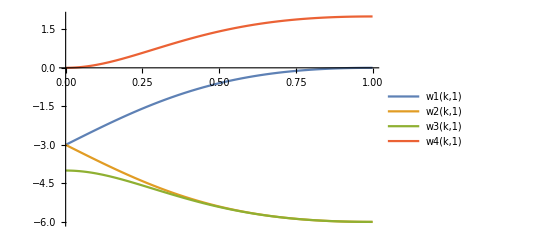

```mathematica
Plot[{w1[k,1],w2[k,1],w3[k,1],w4[k,1]},{k,0,1}, PlotLegends->"Expressions"]
```

```mathematica
Series [Integrate[  
0.5*(D[period[1,k,1,x],x])^2+paper[1,1,period[1,k,1,x]],{x,0,10}],{k,1,3}]
```

1/(√(1+JacobiSN[(10 (1+k))/(√(1+k^2)),k]^2 (-1-(k-1)+O[k-1]^4)))(√(1+JacobiSN[(10 (1+k))/(√(1+k^2)),k]^2 (-1-(k-1)+O[k-1]^4)) (-(20 (k-1))/3+10/3 (k-1)^3+O[k-1]^4)+JacobiDN[(10 (1+k))/(√(1+k^2)),k] (13.3333 (k-1)-6.66667 (k-1)^3+O[k-1]^4)+JacobiCN[(10 (1+k))/(√(1+k^2)),k] JacobiDN[(10 (1+k))/(√(1+k^2)),k] JacobiSN[(10 (1+k))/(√(1+k^2)),k] √(1+JacobiSN[(10 (1+k))/(√(1+k^2)),k]^2 (-1-(k-1)+O[k-1]^4)) (-(√2)/3-1/3 √2 (k-1)+(k-1)^2/(4 √2)+O[k-1]^4)+JacobiCN[(10 (1+k))/(√(1+k^2)),k] JacobiDN[(10 (1+k))/(√(1+k^2)),k] JacobiSN[(10 (1+k))/(√(1+k^2)),k] √(JacobiSN[(10 (1+k))/(√(1+k^2)),k]^2 (-1-(k-1)+O[k-1]^4)+(1-(k-1)+O[k-1]^4)+JacobiCN[(10 (1+k))/(√(1+k^2)),k]^2 (1+(k-1)+O[k-1]^4)) (-0.333333-0.333333 (k-1)+0.125 (k-1)^2-1.38778×10^-17 (k-1)^3+O[k-1]^4)+EllipticE[JacobiAmplitude[(10 (1+k))/(√(1+k^2)),k],k] JacobiDN[(10 (1+k))/(√(1+k^2)),k] (0.471405-0.471405 (k-1)-0.176777 (k-1)^2+0.353553 (k-1)^3+O[k-1]^4)+EllipticE[JacobiAmplitude[(10 (1+k))/(√(1+k^2)),k],k] JacobiDN[(10 (1+k))/(√(1+k^2)),k] (-(2 √2)/3+2/3 √2 (k-1)+(k-1)^2/(2 √2)-(k-1)^3/(√2)+O[k-1]^4)+EllipticE[JacobiAmplitude[(10 (1+k))/(√(1+k^2)),k],k] JacobiDN[(10 (1+k))/(√(1+k^2)),k] (√2-(k-1)^2/(4 √2)+(k-1)^3/(4 √2)+O[k-1]^4))

```mathematica
c[x_,k_]:=x+k
```

```mathematica
c1[k_]:=Integrate[c[x,k],{x,0,1}]
```

```mathematica
Series[c1[k],{k,0,3}]
```

1/2+k+O[k]^4

```mathematica
c1[0]
```

1/2

```mathematica
energyconfig[20,1,1,1]
```

0.942809